# A Mathematica NURBS (Non-Uniform Rational B-Splines) Package and Its Applications

Author: Liutong Zhou
Columbia University

## Chapter 1 Curve and Surface Basics

All the customized functions we showed here are included in the package “NURBS”

```mathematica
Needs["NURBS`"]
```

Package NURBS.wl By Liutong Zhou, Version 1.0
Created on Nov. 25 2016
Last Updated on Dec 11 2016

User-accessible functions:
NDegreePowerBasis,Bernstein, MyBezierCurve, PlotBezierCurve, RationalBezierCurve, PlotRationalBezierCurve,BezierSurface,PlotBezierSurface,
RationalBezierSurface,PlotRationalBezierSurface

Type ?functionname to see usage information

## 1.2 Power Basis Form of a Curve

The n-degree Power Basis Curve is defined by equation (1.6) in the NURBS Book.

C(u)=(x_1 | ... | x_n
y_1 | ... | y_n
z_1 | ... | z_n).(u^0
⋮
u^n), for 0≤u≤1

Here the NDegreePowerBasis is an implementation of it, this function is included in the package "NURBS"

```mathematica
?NDegreePowerBasis
```

NDegreePowerBasis[pts] creates an N Degree Power Basis Curve with control points pts.

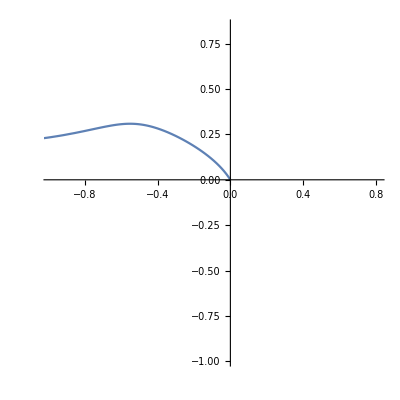
{-Graphics-,-Graphics3D-}

```mathematica
twodpts:=RandomReal[{-1,1},{10,2}]; (*generate some random data points*)
threedpts:=RandomReal[{-1,1},{10,3}];
{NDegreePowerBasis[twodpts],NDegreePowerBasis[threedpts]}(*draw the curve*)
```

## 1.3 Bezier Curves

BezierCurve is an improved version of Power Basis Curve, Mathematica has an in-built Function to implement it, but we can also easily implement it by ourselves. The nth degree Bezier Curve is defined by

C(u)=∑_(i=0)^n BernsteinBasis[n,i,u]P_i , 0≤u≤1

The nth degree BernsteinBasis is nothing but a Binomial Expansion of (1-u+u)^n

BernsteinBasis[n,i,u]=(n
i)u^i(1-u)^(n-i), 0≤u≤1

```mathematica
?BezierCurve
```

RowBox[{"BezierCurve", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] is a graphics primitive that represents a Bézier curve with control points SubscriptBox[StyleBox["pt", "TI"], StyleBox["i", "TI"]].

```mathematica
(*The Mathematica Version of the BezierCurve Plot*)
```

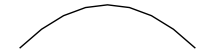

```mathematica
Graphics[BezierCurve[{{0,0},{1,1},{2,0}}]]
```

MyBezierCurve is a function in the package “NURBS”, PlotBezierCurve in the package will plot MyBezierCurve

```mathematica
?Bernstein
```

Bernstein[i, n, v] returns the ith term of the n-degree Bernstein polynomial basis

```mathematica
?MyBezierCurve
```

MyBezierCurve[points,u] Returns the parametric form of the BezierCurve definend by the control points

```mathematica
?PlotBezierCurve
```

PlotBezierCurve[points] plots the BezierCurve defined by the control points

```mathematica
MyBezierCurve[{{0,0},{1,1},{2,0}},u]
```

{2 u,-2 (-1+u) u}

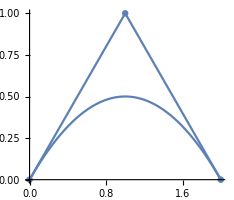

```mathematica
PlotBezierCurve[{{0,0},{1,1},{2,0}}]
```

```mathematica
PlotBezierCurve[{{0,0,1},{1,1,0},{2,0,1},{1,2,3}}]
```

-Graphics3D-

You can also generate the same graphs using the built-in functions. 
Now lets try a closed BezierCurve

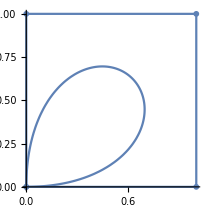

```mathematica
PlotBezierCurve[{{0,0},{0,1},{1,1},{1,0},{0,0}}]
```

## 1.4 Rational Bezier Curves

A rational Bezier Curve is defined in equation (1.18) in the NURBS Book. It makes use of the Homogeneous Coordinates which has a higher dimension and then transformed points are projected back to the space where the control points dwell. A rational Bezier Curve:

C(u)=(∑_(i=0)^n BernsteinBasis[n,i,u]w_i P_i)/(∑_(j=0)^n BernsteinBasis[n,j,u]w_j), 0≤u≤1

Lets show an example (Ex. 1.14) from the NURBS Book using functions from the “NURBS” package

```mathematica
data={{1,0,1},{1,1,1},{0,1,2}};
```

```mathematica
?RationalBezierCurve
```

RationalBezierCurve[points,u] gives the parametric form of the Rational Bezier Curve definend by the control points.\n \nThe last column of points is the weight of the points

```mathematica
RationalBezierCurve[data,u]/.u->1/2
```

{3/5,4/5}

This result is the same as in the book

```mathematica
?PlotRationalBezierCurve
```

PlotRationalBezierCurve[data] plots the RationalBezierCurve[points,u]

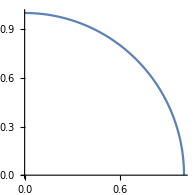
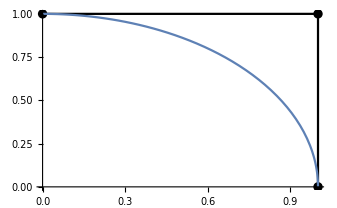
Null -Graphics- -Graphics-

```mathematica
PlotRationalBezierCurve[data]
```

```mathematica
PlotRationalBezierCurve[RandomReal[10,{5,4}]]
```

Null -Graphics3D- -Graphics3D-

## 1.5 Tensor Product Surfaces

Now we move one step further from curves to surfaces. Using the same definition as that (1.20) in the NURBS Book. A tensor product surface has the form

for   i=0,...,n; j=0,...,m          S(u,v)=f_i^T(u) b_(i,j) g_j(v),      0≤ u,v≤1

Here f^T(u) is a 1×(n+1) row vector, b  is a (n+1)×(m+1) matrix and g(v) is a (m+1)×1 column vector. We will see examples below

### 1. PowerBasisSurface

```mathematica
data={{{0,0,0},{1,0,0},{2,0,0}},{{0,1,1},{1,1,1},{2,1,1}},{{0,2,0},{1,2,0},{2,2,0}}};
```

```mathematica
?PowerBasisSurface
```

PowerBasisSurface[points,u,v] gives the Power Basis Surface defined by control points in parametric form S(u,v)

```mathematica
PowerBasisSurface[data,u,v]
```

{(1+u+u^2) v (1+2 v),u (1+2 u) (1+v+v^2),u (1+v+v^2)}

```mathematica
?PlotPowerBasisSurface
```

PlotPowerBasisSurface plots the PowerBasisSurface defined by control points

```mathematica
PlotPowerBasisSurface[data]
```

-Graphics3D-

### 2. Bezier Surface

```mathematica
?BezierSurface
```

BezierSurface[points,u,v] gives out the Bezier Surface S(u,v) defined by the control points in Parametric form

```mathematica
BezierSurface[data,u,v]
```

{2 v,2 u,-2 (-1+u) u}

```mathematica
?PlotBezierSurface
```

PlotBezierSurface[points] plot the Bezier Surface S(u,v) defined by the control ponints

```mathematica
PlotBezierSurface[data]
```

-Graphics3D-

## 1.6 Rational Bezier Surface

A rational Bezier Surface is define by the perspective projection of a four dimensional polynomial Bezier Surface.
Let (P_(i,j))^w be the control point P_(i,j)  weighted in the Homogenous Coordinates, that is

P_(i,j)=(x,y,z)⇒(P_(i,j))^w=(w x,w y,w z,w)

Constructing a Polynomial Bezier Surface in the 4 dimensional Homogenous Coordinates and using the perspective projection to transform the surface back to 3 dimensional space. We get

S(u,v)=H{S^w(u,v)}=(∑_(i=0)^n ∑_(j=0)^m B_(i,n)(u)B_(j,m)(v)w_(i,j)P_(i,j))/(∑_(i=0)^n ∑_(j=0)^m B_(i,n)(u)B_(j,m)(v)w_(i,j))=∑_(i=0)^n ∑_(j=0)^m R_(i,j)(u,v)P_(i,j)

where

R_(i,j)(u,v)=(B_(i,n)(u)B_(j,m)(v)w_(i,j))/(∑_(i=0)^n ∑_(j=0)^m B_(i,n)(u)B_(j,m)(v)w_(i,j))

Rational Bezier Surface is a tensor product surface in the Homogenous Coordinates but is not a tensor product surface in the three dimensional space. 
An implementation of the above is given in the package “NURBS”.

```mathematica
?RationalBezierSurface
```

RationalBezierSurface[points,u,v] gives the parametric form of the Rational Bezier Surface definend by the control points. 
The last column of the points is the weight of the points

```mathematica
data=RandomInteger[3,{3,3,4}];
```

```mathematica
RationalBezierSurface[data,u,v]
```

{(-2 u (6-8 v+v^2)+u^2 (6-8 v+v^2)-2 (-3+2 v+v^2))/(3-6 u (-1+v)^2-2 v+u^2 (5-12 v+7 v^2)),(4 u (2-3 v) v+2 (4-3 v) v+u^2 (6-24 v+20 v^2))/(3-6 u (-1+v)^2-2 v+u^2 (5-12 v+7 v^2)),((4-3 v) v-2 u v (-8+7 v)+u^2 (4-28 v+22 v^2))/(3-6 u (-1+v)^2-2 v+u^2 (5-12 v+7 v^2))}

```mathematica
?PlotRationalBezierSurface
```

PlotRationalBezierSurface[points] plots the RationalBezierSurface[points,u,v]

```mathematica
PlotRationalBezierSurface[data]
```

-Graphics3D-

When all the weights are set to 1, Rational Bezier Surface becomes the same as polynomial Bezier Surface

```mathematica
data=Join[{{{0,0,0},{1,0,0},{2,0,0}},{{0,1,1},{1,1,1},{2,1,1}},{{0,2,0},{1,2,0},{2,2,0}}},ConstantArray[{1},{3,3}],3];
PlotRationalBezierSurface[data]
```

-Graphics3D-